Autocorrelations for Generalised Hybrid Monte Carlo

## Quadratic Operators with Fixed Length Trajectories

Based on the papeτ, “Cost of the Generalised Hybrid Monte Carlo Algorithm for Free Field Theory”, this notebook contains a Mathematica format for selected equations. The aim is to provide a dynamic method of working with the theory.

The paper provides the Laplace Transform of the autocorrelations which will be denoted by F[...] where β is the Laplace transformed time, t

Unless explicitly stated, all equations are in Laplace Transformed format

Throughout the plots, the following parameters will be used:

## Laplace Transformed GHMC Autocorrelation Function

The form is exceedingly long and so has been broken apart into testable segments specified by an[...],

```mathematica
a0[ρ_,ϕ_]:=-ρ Cos[ϕ]^2-1+ρ
a1[θ_,ρ_] := (-1+2ρ)Cos[θ]^3
a2[θ_, ρ_,ϕ_] := (-2ρ+1+2ρ Cos[ϕ]^2)Cos[θ]^2
a3[θ_, ρ_,ϕ_]:=(ρ+ρ Cos[ϕ]^2-1)Cos[θ]
a4[θ_, ρ_,ϕ_]:=(-2ρ Cos[ϕ]^2+1)Cos[θ]+(Cos[θ]^2+1)a0[ρ,ϕ]
a5[θ_, ρ_,ϕ_]:=a3[θ, ρ,ϕ] Cos[θ]^2
a6[θ_, ρ_]:=(1-2ρ)Cos[θ]^3
```

The Laplace Transform of the autocorrelation for quadratic operators is given by,

```mathematica
F[β_, ϕ_, θ_, ρ_, τ_]:=(-(Exp[-βτ]a0[ρ,ϕ]-Exp[-3β τ]a1[θ, ρ]+Exp[-2β τ]a2[θ, ρ,ϕ]+Exp[-2β τ]a3[θ, ρ,ϕ]))/(a4[θ, ρ,ϕ]Exp[-β τ]+a5[θ, ρ,ϕ]Exp[-2β τ]+a6[θ,ρ]Exp[-3β τ]+Exp[-2β τ](a2[θ, ρ,ϕ]+a3[θ, ρ,ϕ])+1)
```

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
a7[θ_, ϕ_]:=(-1+2 Cos[ϕ]^2)Cos[θ]^2
a8[θ_, ϕ_]:=(Cos[ϕ]^2 Cos[θ]^2+(-1+2 Cos[ϕ]^2)Cos[θ]+Cos[ϕ]^2)
a9[θ_, ϕ_]:=a7[θ, ϕ]+Cos[ϕ]^2 Cos[θ]
```

```mathematica
Funit[β_, ϕ_, θ_, τ_]:=(-(Exp[-β τ] Cos[ϕ]^2+Exp[-3β τ] Cos[θ]^3-Exp[-2β τ]a7[θ, ϕ]-Exp[-2β τ] Cos[ϕ]^2 Cos[θ]))/(Exp[-β τ]a8[θ, ϕ]+(Exp[-3β τ]-Exp[-2β τ] Cos[ϕ]^2)Cos[θ]^3-Exp[-2β τ]a9[θ, ϕ]-1)
```

Check This should be equal to Equation (1) for ρ =1:

```mathematica
FullSimplify[Funit[β, ϕ,  θ, τ]==F[β, ϕ, θ, 1, τ]]
```

True

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMC[β_,ϕ_, ρ_, τ_]:= (-a0[ρ,ϕ])/(Exp[β τ]+a0[ρ,ϕ])
```

Check This should be equal to Equation (1) for θ = π/2:

```mathematica
FullSimplify[F[β, ϕ, π/2, ρ, τ]==FHMC[β,ϕ,ρ, τ]]
```

True

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMCunit[β_, ϕ_, τ_] :=Cos[ϕ]^2/(Exp[β τ]-Cos[ϕ]^2)
```

Check This should be equal to Equation (1) for ρ = 1 and θ=π/2:

```mathematica
FullSimplify[FHMCunit[β, ϕ, τ]==F[β, ϕ, π/2, 1,τ]]
```

True

## Regular GHMC Integrated Autocorrelation Function

The integrated autocorrelation for GHMC is obtained by setting β = 0 for the autocorrelation in Equation (1). As it no longer contains a dependancy upon β, this is also equivalent to the Inverse Laplace Transform i.e. the non-Transformed Integrated Autocorrelation Function,

```mathematica
A[ϕ_, θ_, ρ_]:=-((1-2ρ )Cos[θ]^2+2Cos[θ]ρ Cos[ϕ]^2-ρ Cos[ϕ]^2-1+ρ)/((Cos[θ]-1)(Cos[θ]+1)(Cos[ϕ]-1)(Cos[ϕ]+1)ρ)
```

Check This should be equal to Equation (1) for β=0:

```mathematica
FullSimplify[A[ϕ, θ, ρ] == F[0, ϕ, θ, ρ, τ]]
```

True

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
Aunit[ϕ_, θ_]:=(Cos[θ]^2-2Cos[θ] Cos[ϕ]^2+Cos[ϕ]^2)/(Cos[θ]^2 Cos[ϕ]^2-Cos[θ]^2-Cos[ϕ]^2+1)
```

Check This should be equal to Equation (1) for ρ=1 and β=0:

```mathematica
FullSimplify[Aunit[ϕ, θ]==F[0, ϕ, θ, 1, τ]]
```

True

The integrated autocorrelation under unit acceptance varying with mixing angle,

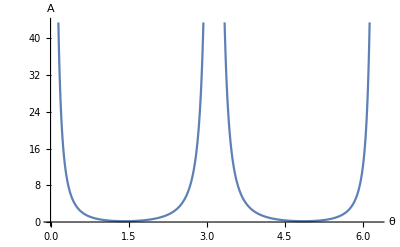

```mathematica
Plot[Aunit[τ, θ], {θ, 0, 2π},AxesLabel->{"θ","A"}]
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMC[ϕ_, ρ_]:=(-a0[ρ,ϕ])/(ρ(1- Cos[ϕ])(1+Cos[ϕ]))
```

Check This should be equal to Equation (1) for θ = π/2 and β=0:

```mathematica
FullSimplify[F[0,ϕ, π/2, ρ, τ] == AHMC[ϕ, ρ]]
```

True

Showing the change in the HMC integrated autocorrelation varying with acceptance rate,

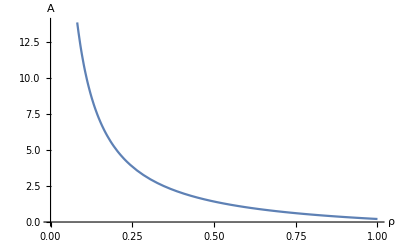

```mathematica
Plot[A[τ, π/2,ρ],{ρ, 0, 1},AxesLabel->{"ρ","A"}]
```

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMCunit[ϕ_] :=Cos[ϕ]^2/(1-Cos[ϕ]^2)
```

Check This should be equal to Equation (1) for θ=π/2, β=0 and ρ=1:

```mathematica
FullSimplify[AHMCunit[ϕ]==F[0, ϕ, π/2, 1, τ]]
```

True

## Inverse Laplace Transforms: Regular GHMC Autocorrelations

Inverting the autocorrelation functions gets very messy and so starting in reverse order now makes more sense, leaving the most complicated for last.

There is a sepcific method provided in the paper howeveτ, partial fraction decomposition is not well supported in Mathematica so it makes more sense to simply force the result for those that are no immediately obvious.

## HMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMCunit = InverseLaplaceTransform[FHMCunit[β ,ϕ, τ],β,t] //ToRadicals // FullSimplify
```

Cos[ϕ]^2 InverseLaplaceTransform[1/(ⅇ^(2. β)-Cos[ϕ]^2),β,t]

```mathematica
CHMCunit[t_, ϕ_,τ_ ] := Evaluate[iFHMCunit]
```

Plotting shows the underdamped form for unit mass and averge trajector length τ,

```mathematica
Plot[CHMCunit[t, τ, 1/τ], {t, 0, 50},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

-Graphics-

### HMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMC = InverseLaplaceTransform[FHMC[β ,ϕ, ρ, τ],β,t] //ToRadicals //FullSimplify
```

(1-ρ+ρ Cos[ϕ]^2) InverseLaplaceTransform[1/(-1+ⅇ^(2. β)+ρ-ρ Cos[ϕ]^2),β,t]

```mathematica
CHMC[t_, ϕ_, ρ_, τ_ ] := Evaluate[iFHMC]
```

Plotting for varying acceptance rate at t=0,

```mathematica
Plot[CHMC[0, τ, 1/ρ, τ], {ρ, 0, 1},PlotRange->{0,1},AxesLabel->{"ρ","C(0)"}]
```

-Graphics-

## GHMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFunit = InverseLaplaceTransform[Funit[β, ϕ, θ, τ],β,t] //ToRadicals
```

-InverseLaplaceTransform[(ⅇ^(-6. β) Cos[θ]^3+ⅇ^(-2. β) Cos[ϕ]^2-ⅇ^(-4. β) Cos[θ] Cos[ϕ]^2-ⅇ^(-4. β) Cos[θ]^2 (-1+2 Cos[ϕ]^2))/(-1+Cos[θ]^3 (ⅇ^(-6. β)-ⅇ^(-4. β) Cos[ϕ]^2)+ⅇ^(-2. β) (Cos[ϕ]^2+Cos[θ]^2 Cos[ϕ]^2+Cos[θ] (-1+2 Cos[ϕ]^2))-ⅇ^(-4. β) (Cos[θ] Cos[ϕ]^2+Cos[θ]^2 (-1+2 Cos[ϕ]^2))),β,t]

```mathematica
Cunit[t_, ϕ_, θ_, τ_] := Evaluate[iFunit]
```

varying with mixing angle θ,

```mathematica
Plot3D[Cunit[t,τ,θ,1/τ],{t,0,50},{θ,0.15π,2 π-0.15π},PlotTheme->"Scientific",PlotRange->{0,1},AxesLabel->{"t","θ","C(t)"}]
```

-Graphics3D-

### GHMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iF = InverseLaplaceTransform[F[β, ϕ, θ, ρ, τ],β,t] //ToRadicals
```

-InverseLaplaceTransform[(-ⅇ^(-6. β) (-1+2 ρ) Cos[θ]^3+ⅇ^(-2. β) (-1+ρ-ρ Cos[ϕ]^2)+ⅇ^(-4. β) Cos[θ] (-1+ρ+ρ Cos[ϕ]^2)+ⅇ^(-4. β) Cos[θ]^2 (1-2 ρ+2 ρ Cos[ϕ]^2))/(1+ⅇ^(-6. β) (1-2 ρ) Cos[θ]^3+ⅇ^(-4. β) Cos[θ]^3 (-1+ρ+ρ Cos[ϕ]^2)+ⅇ^(-2. β) (Cos[θ] (1-2 ρ Cos[ϕ]^2)+(1+Cos[θ]^2) (-1+ρ-ρ Cos[ϕ]^2))+ⅇ^(-4. β) (Cos[θ] (-1+ρ+ρ Cos[ϕ]^2)+Cos[θ]^2 (1-2 ρ+2 ρ Cos[ϕ]^2))),β,t]

```mathematica
CF[t_, ϕ_, θ_,  ρ_, τ_] := Evaluate[iF]
```

varying with mixing angle θ and acceptance probability,

```mathematica
Plot3D[CF[t,τ,π/4,1/τ,ρ ],{t,0,50},{ρ ,0.6,1},PlotTheme->"Scientific",PlotRange->{0,1},AxesLabel->{"t","ρ","C(t)"}]
```

-Graphics3D-

```mathematica
DumpSave["dump.mx", "Global`"]
```